```mathematica
τm=10 ;El=-70;Rm=10;Vth=-54;Vreset=-80;Vspike=0;
```

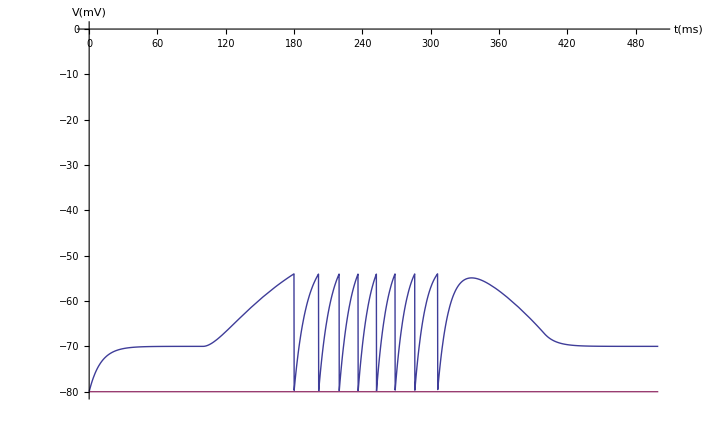

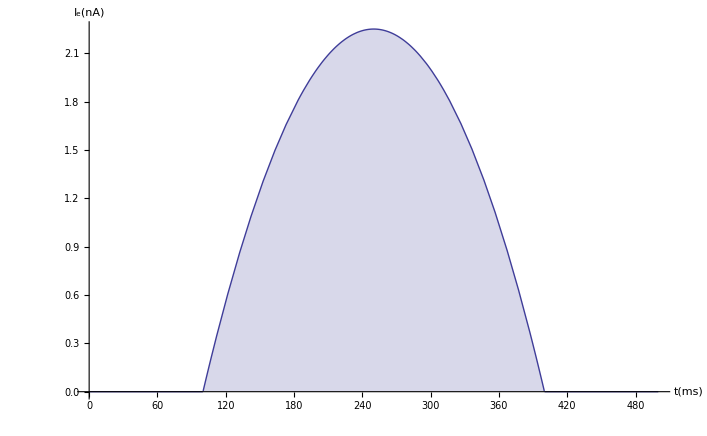

```mathematica
ClearAll["Global`*"];
τm=10 ;El=-70;Rm=10;Vth=-54;Vreset=-80;Vspike=0;
Ie[t_]:=Piecewise[{{-(t-100)(t-400)/10000,t>=100&&t<=400}},0];
res=NDSolve[{τm V'[t]==-V[t]+El+Rm Ie[t],V[0]==Vreset,WhenEvent[V[t]==Vth,V[t]->Vreset]},V,{t,0,500}];
spike[v_]:=Piecewise[{{0,v==Vth||v==Vreset}},Vreset];
Plot[{Evaluate[V[t]/.res],spike[Evaluate[V[t]/.res][[1]]]},{t,0,500},PlotRange->{-80,0},AxesLabel->{"t(ms)","V(mV)"}]
Plot[Ie[t],{t,0,500},Filling->Axis,AxesLabel->{"t(ms)","I_e(nA)"}]
```

```mathematica
Risi[ie_]:=N[Piecewise[{{(τm Log[(Rm ie+El-Vreset)/(Rm ie+El-Vth)])^-1,Rm ie>Vth-El}},0]]
```

```mathematica
calcFiringRate[iec_]:=Module[{spikeCount},τm=10 ;El=-70;Rm=10;Vth=-54;Vreset=-80;Vspike=0;
Iec[t_]:=Piecewise[{{iec,t>=100&&t<=400}},0];
spikeCount=0;
resC=NDSolve[{τm V'[t]==-V[t]+El+Rm Iec[t],V[0]==Vreset,WhenEvent[V[t]==Vth,{V[t]->Vreset,spikeCount+=1}]},V,{t,0,500}];
spike[v_]:=Piecewise[{{0,v==Vth||v==Vreset}},Vreset];
firingRate1=N[spikeCount/300];
firingRate2=Risi[iec];
{firingRate1,firingRate2}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 397.398.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 393.17.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 389.061.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

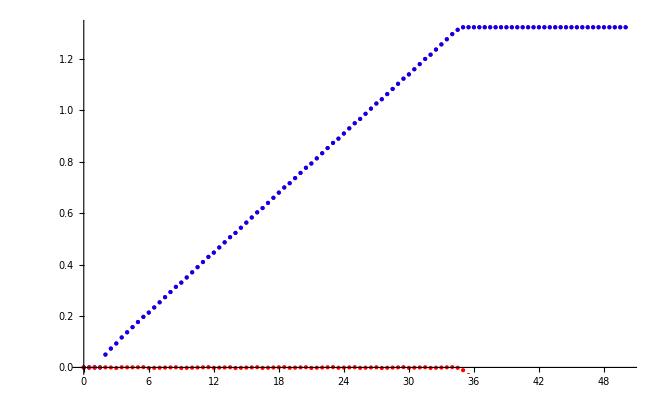

```mathematica
iecTable=Table[i,{i,0,50,0.5}];
frs=Map[calcFiringRate[#]&,iecTable];
Show[ListPlot[MapThread[List,{iecTable,Map[#[[1]]&,frs]}],PlotStyle->Green],ListPlot[MapThread[List,{iecTable,Map[#[[1]]&,frs]}],PlotStyle-> Blue],ListPlot[MapThread[List,{iecTable,Map[#[[1]]-#[[2]]&,frs]}],PlotStyle->Red]]
```

```mathematica
Map[#[[1]]-#[[2]]&,frs]
```

{0.,0.,0.,0.,0.00036982,-0.000297674,-0.0019209,0.000687459,0.000421163,0.000425786,0.000605381,0.000905148,-0.00204205,-0.00159164,-0.00109202,-0.000553867,0.0000150536,0.000608941,-0.00210996,-0.00147841,-0.000832446,-0.000174229,0.000494494,0.00117229,-0.00147535,-0.000782737,-0.0000840418,0.00062004,-0.00200442,-0.00129127,-0.000574273,0.000146178,0.000869754,-0.00173717,-0.00100818,-0.000276847,0.000456641,0.0011921,-0.00140396,-0.000665017,0.0000754699,0.000817384,-0.00177271,-0.00102824,-0.00028263,0.00046405,0.00121173,-0.001373,-0.000623522,0.000126776,0.000877842,-0.0017037,-0.000951235,-0.000198125,0.000555589,-0.00202346,-0.00126863,-0.000513294,0.000242529,0.000998812,-0.0015778,-0.000820667,-0.0000631384,0.000694766,-0.0018803,-0.0011217,-0.000362772,0.000396467,0.001156,-0.00141751,-0.0106574,-0.0298971,-0.0491365,-0.0683756,-0.0876146,-0.106853,-0.126092,-0.14533,-0.164568,-0.183806,-0.203044,-0.222281,-0.241519,-0.260756,-0.279993,-0.29923,-0.318467,-0.337703,-0.35694,-0.376176,-0.395413,-0.414649,-0.433885,-0.453121,-0.472356,-0.491592,-0.510828,-0.530063,-0.549299,-0.568534,-0.587769}

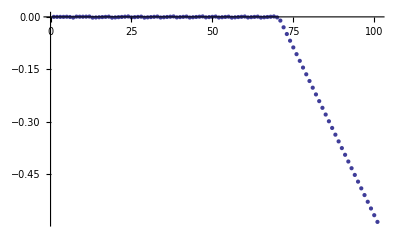

```mathematica
ListPlot[Map[#[[1]]-#[[2]]&,frs]]
```

```mathematica
Show[ListPlot[MapThread[List,{iecTable,Map[#[[1]]&,frs]}],PlotStyle->Green,PlotMarkers->{"●",3},PlotLegends->{"Real Firing Rate"},AxesLabel->{"Constant I_e(nA)","Firing Rate"}],ListPlot[MapThread[List,{iecTable,Map[#[[1]]&,frs]}],PlotStyle-> Blue,PlotMarkers->{"●",1},PlotLegends->{"R_isi Firing Rate"}],ListPlot[MapThread[List,{iecTable,Map[#[[1]]-#[[2]]&,frs]}],PlotStyle->Red,PlotMarkers->{"●",3},PlotLegends->{"Error"}]]
```

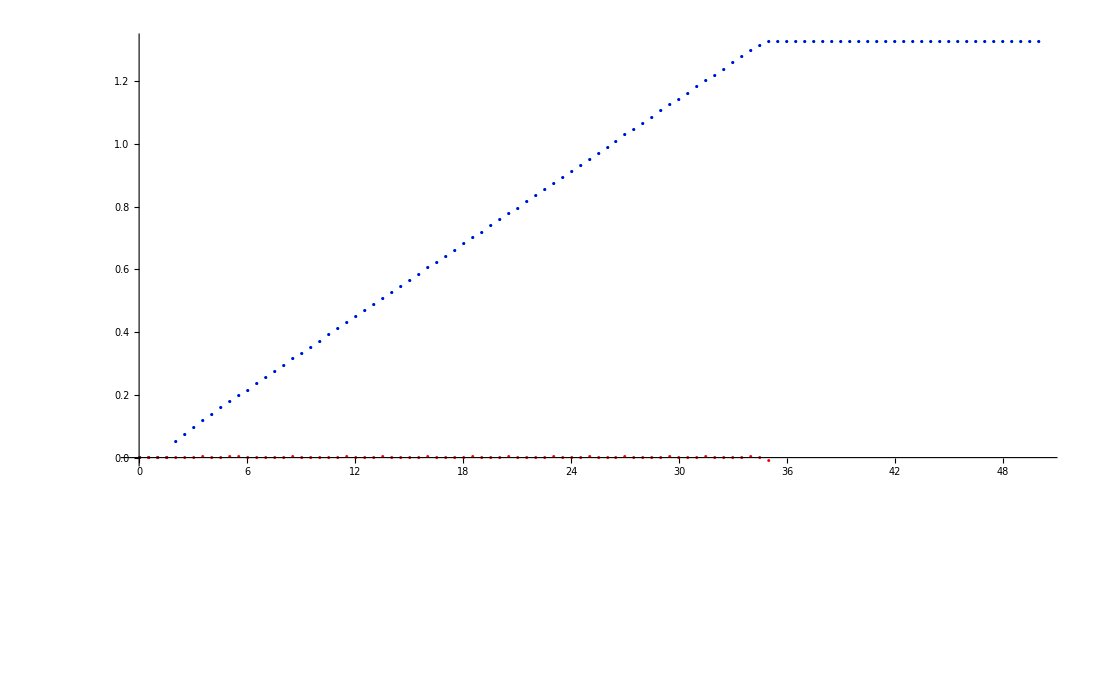

```mathematica
ClearAll["Global`*"];
glbar=0.003;gkbar=0.36;gnabar=1.2;El=-54.387;Ek=-77;Ena=50;cm=10;
αm[V_]:=(0.1(V+40))/(1-ⅇ^(-0.1(V+40)));βm[V_]:=4 ⅇ^(-0.0556(V+65));αh[V_]:=0.07 ⅇ^(-0.05(V+65));βh[V_]:=1/(1+ⅇ^(-0.1(V+35)));αn[V_]:=(0.01(V+55))/(1-ⅇ^(-0.1(V+55)));βn[V_]:=0.125 ⅇ^(-0.0125(V+65));
```

```mathematica
IeA[t_]:=Piecewise[{{0.2,t≥5&&t≤500}},0];
funcs=NDSolve[{0.001 cm V'[t]==IeA[t]-gnabar h[t] (m[t])^3 (V[t]-Ena)-glbar(V[t]-El)-gkbar (n[t])^4 (V[t]-Ek),m'[t]==αm[V[t]](1-m[t])-βm[V[t]] m[t],
h'[t]==αh[V[t]](1-h[t])-βh[V[t]] h[t],
n'[t]==αn[V[t]] (1-n[t])-βn[V[t]] n[t]
,V[0]==-65,m[0]==0.0529,h[0]==0.5961,n[0]==0.3177},{V,m,h,n},{t,0,200}]
```

{{V→InterpolatingFunction[{{0.,200.}},<>],m→InterpolatingFunction[{{0.,200.}},<>],h→InterpolatingFunction[{{0.,200.}},<>],n→InterpolatingFunction[{{0.,200.}},<>]}}

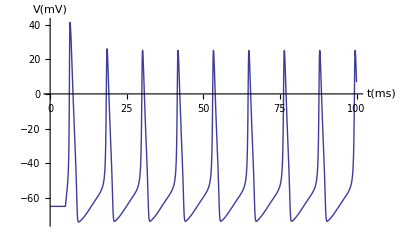

```mathematica
Plot[{Evaluate[V[t]/.funcs[[1]][[1]]]},{t,0,100},AxesLabel->{"t(ms)","V(mV)"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

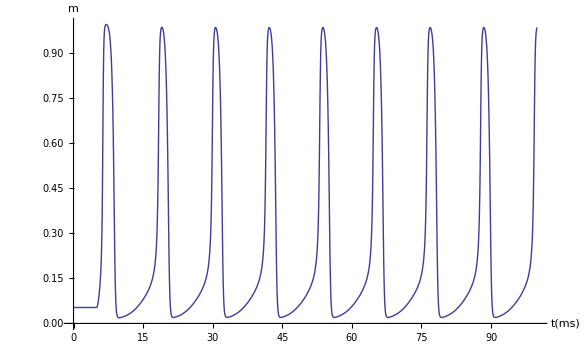

```mathematica
Plot[{Evaluate[m[t]/.funcs[[1]][[2]]]},{t,0,100},AxesLabel->{"t(ms)","m"},BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

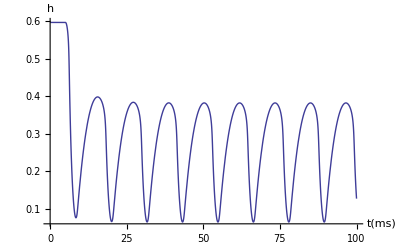

```mathematica
Plot[{Evaluate[h[t]/.funcs[[1]][[3]]]},{t,0,100},AxesLabel->{"t(ms)","h"},BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

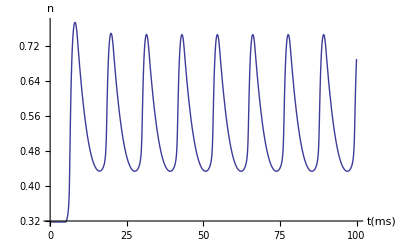

```mathematica
Plot[{Evaluate[n[t]/.funcs[[1]][[4]]]},{t,0,100},AxesLabel->{"t(ms)","n"},PlotRange->{Full,Automatic},BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

```mathematica
funciea[iea_]:=Module[{},IeA[t_]:=Piecewise[{{iea/1000,t>=0&&t≤500}},0];
funcs=NDSolve[{0.001 cm V'[t]==IeA[t]-gnabar h[t] (m[t])^3 (V[t]-Ena)-glbar(V[t]-El)-gkbar (n[t])^4 (V[t]-Ek),m'[t]==αm[V[t]](1-m[t])-βm[V[t]] m[t],
h'[t]==αh[V[t]](1-h[t])-βh[V[t]] h[t],
n'[t]==αn[V[t]] (1-n[t])-βn[V[t]] n[t]
,V[0]==-65,m[0]==0.0529,h[0]==0.5961,n[0]==0.3177},{V,m,h,n},{t,0,100}]]
```

```mathematica
resList=Map[funciea[#]&,Range[0,500,1]]
```

{{{V→InterpolatingFunction[{{0.,100.}},<>],m→InterpolatingFunction[{{0.,100.}},<>],h→InterpolatingFunction[{{0.,100.}},<>],n→InterpolatingFunction[{{0.,100.}},<>]}},«499»,{{V→InterpolatingFunction[{{0.,100.}},<>],m→InterpolatingFunction[{{0.,100.}},<>],h→«21»[{{«1»}},«4»],n→InterpolatingFunction[{{0.,100.}},<>]}}}

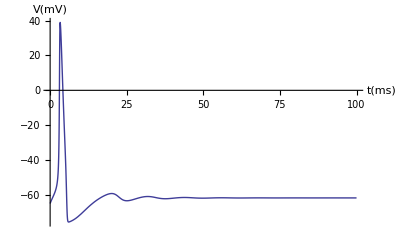
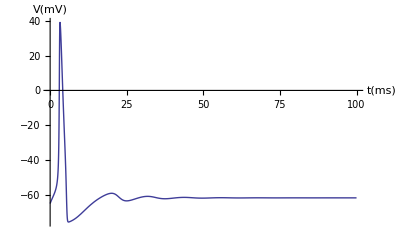
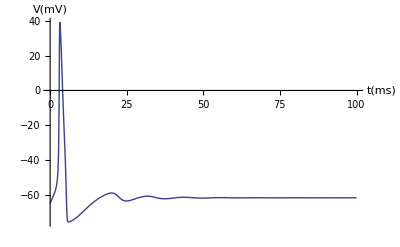
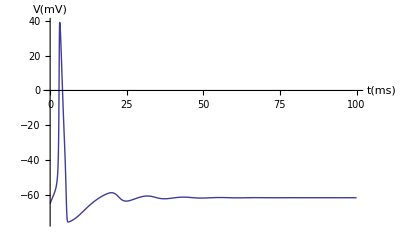
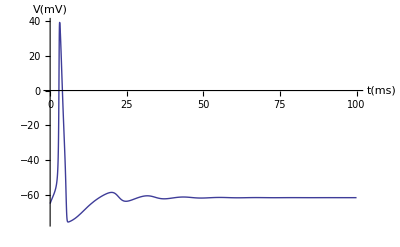
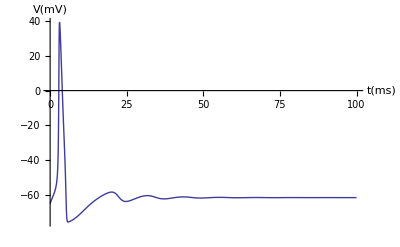
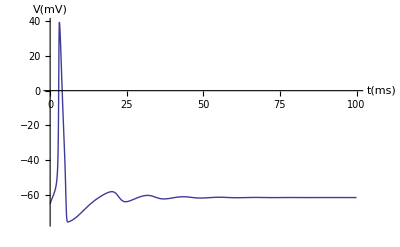
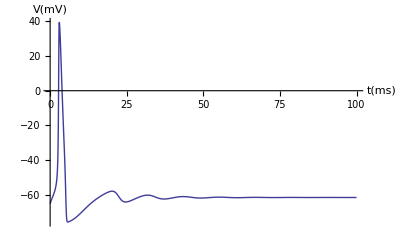

```mathematica
Map[Plot[{Evaluate[V[t]/.#[[1]][[1]]]},{t,0,100},AxesLabel->{"t(ms)","V(mV)"},PlotRange->All]&,resList[[Range[50,100]]]]
```

```mathematica
resList[[1]]
```

{{V→InterpolatingFunction[{{0.,100.}},<>],m→InterpolatingFunction[{{0.,100.}},<>],h→InterpolatingFunction[{{0.,100.}},<>],n→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
Vf1=V/.First[resList[[1]]]
```

InterpolatingFunction[{{0.,100.}},<>]

```mathematica
Vf=Map[V/.First[resList[[#]]]&,Range[1,500]];
```

```mathematica
valueList=Vf[[20]][Range[1,100,0.1]];
tList=Range[1,100,0.1];
dataList=Transpose[{tList,valueList}];
```

```mathematica
maxs=Pick[dataList,MaxDetect[dataList[[All,2]]],1]
```

{{4.8,-60.5383},{18.1,-63.1919},{32.,-63.5128},{46.,-63.5461},{60.,-63.5494},{74.1,-63.5497},{74.2,-63.5497},{88.,-63.5498},{88.1,-63.5498}}

```mathematica
Select[maxs,#[[2]]>0&]
```

{}

```mathematica
calcFiringRate2[Iea_,tList_]:=Module[{valueList,dataList,maxs,realSpike},valueList=Vf[[Iea]][tList];
dataList=Transpose[{tList,valueList}];maxs=Pick[dataList,MaxDetect[dataList[[All,2]]],1];realSpike=Select[maxs,#[[2]]>0&];Length[realSpike]];
```

```mathematica
calcFiringRate2[30,tList]
```

1

```mathematica
Ilist=Range[1,500];
```

```mathematica
frs2=Map[N[calcFiringRate2[#,tList]/100]&,Ilist]
frs2[[23]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.04,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12}

0.

```mathematica
ifrsList=Transpose[{Ilist,frs2}];
```

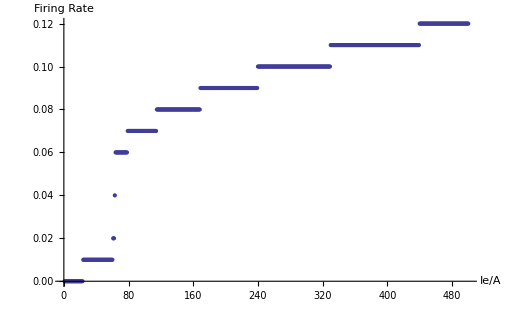

```mathematica
ListPlot[ifrsList,BaseStyle->{FontWeight-> "Bold",FontSize->14},AxesLabel->{"Ie/A","Firing Rate"}]
```

```mathematica
IeA[t_]:=Piecewise[{{-50/1000,t≥5&&t≤10}},0];
funcs3=NDSolve[{0.001 cm V'[t]==IeA[t]-gnabar h[t] (m[t])^3 (V[t]-Ena)-glbar(V[t]-El)-gkbar (n[t])^4 (V[t]-Ek),m'[t]==αm[V[t]](1-m[t])-βm[V[t]] m[t],
h'[t]==αh[V[t]](1-h[t])-βh[V[t]] h[t],
n'[t]==αn[V[t]] (1-n[t])-βn[V[t]] n[t]
,V[0]==-65,m[0]==0.0529,h[0]==0.5961,n[0]==0.3177},{V,m,h,n},{t,0,100}]
```

{{V→InterpolatingFunction[{{0.,100.}},<>],m→InterpolatingFunction[{{0.,100.}},<>],h→InterpolatingFunction[{{0.,100.}},<>],n→InterpolatingFunction[{{0.,100.}},<>]}}

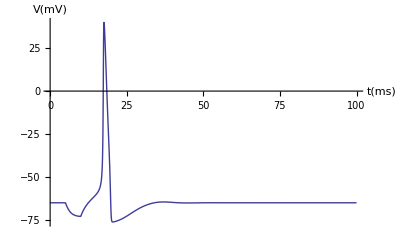

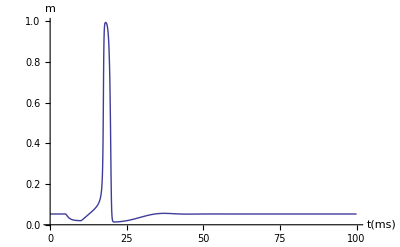

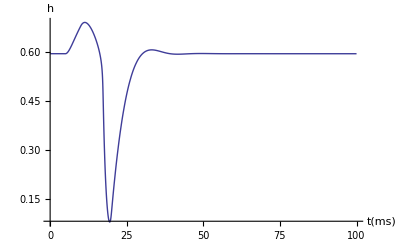

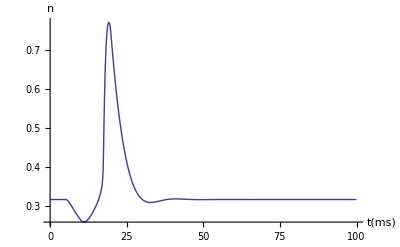

```mathematica
Plot[{Evaluate[V[t]/.funcs3[[1]][[1]]]},{t,0,100},AxesLabel->{"t(ms)","V(mV)"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[m[t]/.funcs3[[1]][[2]]]},{t,0,100},AxesLabel->{"t(ms)","m"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[h[t]/.funcs3[[1]][[3]]]},{t,0,100},AxesLabel->{"t(ms)","h"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[n[t]/.funcs3[[1]][[4]]]},{t,0,100},AxesLabel->{"t(ms)","n"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

```mathematica
3 ConnorStevens
```

```mathematica
TheseFollowing are wrong
minf[V_]:=1/(1+ⅇ^((-(V+57))/6.2));τm[V_]:=0.612+(ⅇ^(-(V+132)/16.7)+ⅇ^((V+16.8)/18.2))^-1;
hinf[V_]:=1/(1+ⅇ^((V+81)/4));τh[V_]:=Piecewise[{{ⅇ^((V+467)/66.6),V<-80},{28+ⅇ^(-(V+22)/10.5),V≥-80}}];
```

```mathematica
ClearAll["Global`*"];
glbar=0.003;gkbar=0.2;gnabar=1.2;El=-17;Ek=-72;gAbar=0.477;Ena=55;cm=10;EA=-75;
αm[V_]:=(0.38(V+29.7))/(1-ⅇ^(-0.1(V+29.7)));βm[V_]:=15.2 ⅇ^(-0.0556(V+54.7));αh[V_]:=0.266 ⅇ^(-0.05(V+48));βh[V_]:=3.8/(1+ⅇ^(-0.1(V+18)));αn[V_]:=(0.02(V+45.7))/(1-ⅇ^(-0.1(V+45.7)));βn[V_]:=0.25 ⅇ^(-0.0125(V+55.7));
im[V_,n_,m_,h_,a_,b_]:=gnabar h m^3 (V-Ena)+glbar (V-El)+gkbar n^4 (V-Ek)+gAbar a^3 b(V-EA);
ninf[V_]:=αn[V]/(αn[V]+βn[V]);τn[V_]:=1/(αn[V]+βn[V]);

minf[V_]:=αm[V]/(αm[V]+βm[V]);τm[V_]:=1/(αm[V]+βm[V]);
hinf[V_]:=αh[V]/(αh[V]+βh[V]);τh[V_]:=1/(αh[V]+βh[V]);

ainf[V_]:=((0.0761 ⅇ^(0.0314(V+94.22)))/(1+ⅇ^(0.0346(V+1.17))))^(1/3);τa[V_]:=0.3632+1.158/(1+ⅇ^(0.0497(V+55.96)));
binf[V_]:=(1/(1+ⅇ^(0.0688(V+53.3))))^4;τb[V_]:=1.24+2.678/(1+ⅇ^(0.0624(V+50)));
```

```mathematica
IeA31[t_]:=Piecewise[{{200/1000,t≥0&&t≤500}},0];
funcs31=NDSolve[{ 0.001 cm V'[t]==IeA31[t]-im[V[t],n[t],m[t],h[t],a[t],b[t]],τm[V[t]] m'[t]==minf[V[t]]-m[t],
τh[V[t]] h'[t]==hinf[V[t]]-h[t],
τn[V[t]] n'[t]==ninf[V[t]]-n[t],
τa[V[t]] a'[t]==ainf[V[t]]-a[t],
τb[V[t]] b'[t]==binf[V[t]]-b[t]
,V[0]==-68,m[0]==0.0101,h[0]==0.9659,n[0]==0.1559,a[0]==0.5404,b[0]==0.2887},{V,m,h,n,a,b},{t,0,100}]
```

{{V→InterpolatingFunction[{{0.,100.}},<>],m→InterpolatingFunction[{{0.,100.}},<>],h→InterpolatingFunction[{{0.,100.}},<>],n→InterpolatingFunction[{{0.,100.}},<>],a→InterpolatingFunction[{{0.,100.}},<>],b→InterpolatingFunction[{{0.,100.}},<>]}}

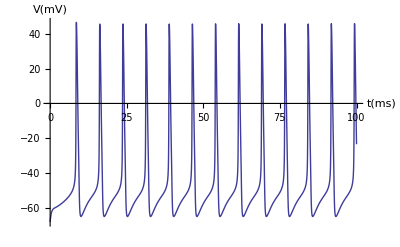

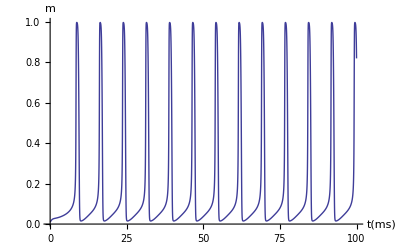

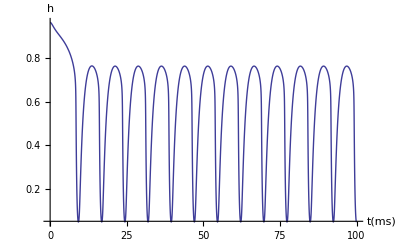

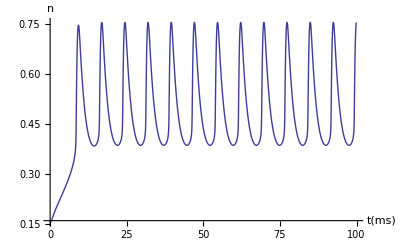

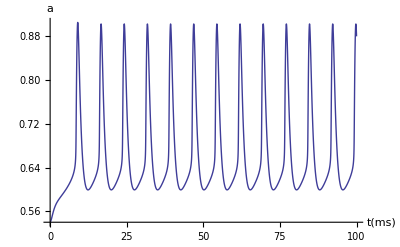

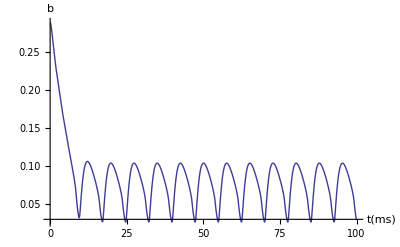

```mathematica
Plot[{Evaluate[V[t]/.funcs31[[1]][[1]]]},{t,0,100},AxesLabel->{"t(ms)","V(mV)"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[m[t]/.funcs31[[1]][[2]]]},{t,0,100},AxesLabel->{"t(ms)","m"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[h[t]/.funcs31[[1]][[3]]]},{t,0,100},AxesLabel->{"t(ms)","h"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[n[t]/.funcs31[[1]][[4]]]},{t,0,100},AxesLabel->{"t(ms)","n"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[a[t]/.funcs31[[1]][[5]]]},{t,0,100},AxesLabel->{"t(ms)","a"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[b[t]/.funcs31[[1]][[6]]]},{t,0,100},AxesLabel->{"t(ms)","b"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```

```mathematica
funciea32[iea_]:=Module[{funcs32,IeA32},IeA32[t_]:=Piecewise[{{iea/1000,t>=0&&t≤200}},0];
funcs32=NDSolve[{ 0.001 cm V'[t]==IeA32[t]-im[V[t],n[t],m[t],h[t],a[t],b[t]],τm[V[t]] m'[t]==minf[V[t]]-m[t],
τh[V[t]] h'[t]==hinf[V[t]]-h[t],
τn[V[t]] n'[t]==ninf[V[t]]-n[t],
τa[V[t]] a'[t]==ainf[V[t]]-a[t],
τb[V[t]] b'[t]==binf[V[t]]-b[t]
,V[0]==-68,m[0]==0.0101,h[0]==0.9659,n[0]==0.1559,a[0]==0.5404,b[0]==0.2887},{V,m,h,n,a,b},{t,0,100}]]
```

```mathematica
resList32=Map[funciea32[#]&,Range[1,500,1]];
```

```mathematica
Vf32=Map[V/.First[resList32[[#]]]&,Range[1,500]];
```

```mathematica
tList32=Range[1,100,0.1];
```

```mathematica
calcFiringRate3[Iea_,tList_]:=Module[{valueList,dataList,maxs,realSpike},valueList=Vf32[[Iea]][tList];
dataList=Transpose[{tList,valueList}];maxs=Pick[dataList,MaxDetect[dataList[[All,2]]],1];realSpike=Select[maxs,#[[2]]>0&];Length[realSpike]];
```

```mathematica
calcFiringRate3[300,tList32]
```

19

```mathematica
Ilist32=Range[1,500];
```

```mathematica
frs3=Map[N[calcFiringRate3[#,tList32]/100]&,Ilist32]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.01,0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.11,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.12,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.18,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.19,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.22,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.23,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.26,0.27}

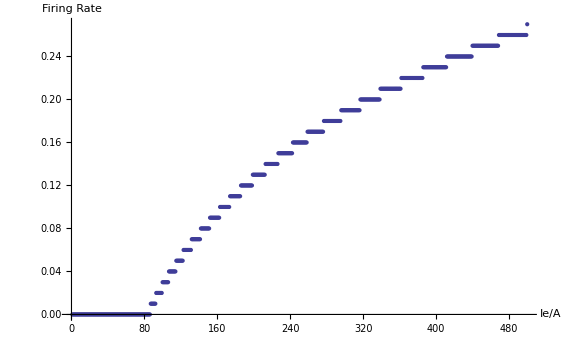

```mathematica
ifrsList32=Transpose[{Ilist32,frs3}];
ListPlot[ifrsList32,BaseStyle->{FontSize->15},AxesLabel->{"Ie/A","Firing Rate"}]
```

```mathematica
IeA33[t_]:=Piecewise[{{-500/1000,t≥ 5&&t≤ 10},{200/1000,t>10}},0];
funcs33=NDSolve[{0.001cm V'[t]==IeA33[t]-im[V[t],n[t],m[t],h[t],a[t],b[t]],τm[V[t]] m'[t]==minf[V[t]]-m[t],
τh[V[t]] h'[t]==hinf[V[t]]-h[t],
τn[V[t]] n'[t]==ninf[V[t]]-n[t],
τa[V[t]] a'[t]==ainf[V[t]]-a[t],
τb[V[t]] b'[t]==binf[V[t]]-b[t]
,V[0]==-68,m[0]==0.0101,h[0]==0.9659,n[0]==0.1559,a[0]==0.5404,b[0]==0.2887},{V,m,h,n,a,b},{t,0,100}]
```

{{V→InterpolatingFunction[{{0.,100.}},<>],m→InterpolatingFunction[{{0.,100.}},<>],h→InterpolatingFunction[{{0.,100.}},<>],n→InterpolatingFunction[{{0.,100.}},<>],a→InterpolatingFunction[{{0.,100.}},<>],b→InterpolatingFunction[{{0.,100.}},<>]}}

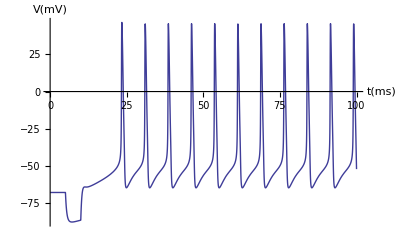

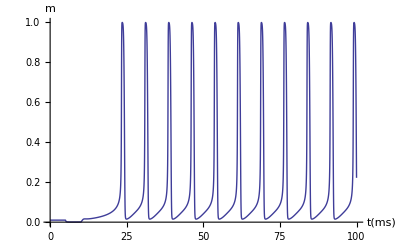

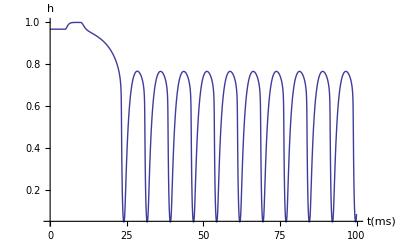

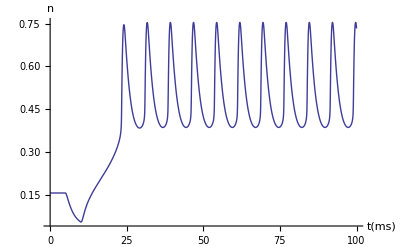

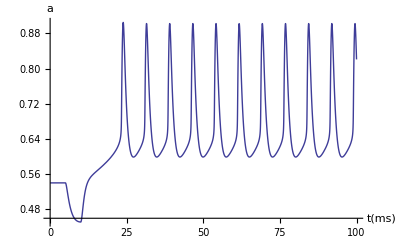

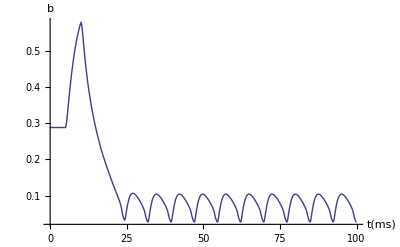

```mathematica
Plot[{Evaluate[V[t]/.funcs33[[1]][[1]]]},{t,0,100},AxesLabel->{"t(ms)","V(mV)"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[m[t]/.funcs33[[1]][[2]]]},{t,0,100},AxesLabel->{"t(ms)","m"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[h[t]/.funcs33[[1]][[3]]]},{t,0,100},AxesLabel->{"t(ms)","h"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[n[t]/.funcs33[[1]][[4]]]},{t,0,100},AxesLabel->{"t(ms)","n"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[a[t]/.funcs33[[1]][[5]]]},{t,0,100},AxesLabel->{"t(ms)","a"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
Plot[{Evaluate[b[t]/.funcs33[[1]][[6]]]},{t,0,100},AxesLabel->{"t(ms)","b"},PlotRange->All,BaseStyle->{FontWeight-> "Bold",FontSize->14}]
```